```mathematica
DSolve[y'[x]+x y[x] == x,y[x],x]
```

DSolve::dsfun: 1+ⅇ^(-x^2/2) cannot be used as a function.

DSolve[-ⅇ^(-x^2/2) x+(1+ⅇ^(-x^2/2)) x==x,1+ⅇ^(-x^2/2),x]

```mathematica
y[x_]:=1+ⅇ^(-x^2/2)
```

```mathematica
FullSimplify[D[y[x],x]]
```

-ⅇ^(-x^2/2) x

```mathematica
FullSimplify[D[y[x],{x,2}]]
```

ⅇ^(-x^2/2) (-1+x^2)

```mathematica
ya[x_]:=1+ⅇ^(-x^2/2)
```

```mathematica
dyadx[x_]:=-ⅇ^(-x^2/2) x
```

```mathematica
d2yadx2[x_]:=ⅇ^(-x^2/2)(x^2-1)
```

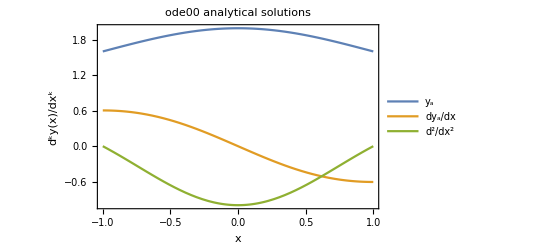

```mathematica
Plot[{ya[x],dyadx[x],d2yadx2[x]},{x,-1,1},AxesLabel->{"x","d^ky(x)/dx^k"},PlotLegends->{"y_a","dy_a/dx","d^2/dx^2"},PlotLabel->"ode00 analytical solutions",Frame->True]
```